# A Machine Learning Analysis of Halting in the SKI Combinator Calculus

Euan Ong

Wolfram High School Summer Camp 2018

Much of machine learning is driven by the question: can we learn what we cannot compute? The learnability of the halting problem, the canonical undecidable problem, to an arbitrarily high accuracy for Turing machines was proven by Lathrop. The SKI combinator calculus can be seen as a reduced form of the untyped lambda calculus, which is Turing-complete; hence, the SKI combinator calculus forms a universal model of computation. In this vein, the growth and halting times of SKI combinator expressions is analysed and the feasibility of a machine learning approach to predicting whether a given SKI combinator expression is likely to halt is investigated.

Keywords: Machine learning, halting problem, SKI combinator calculus.

## SK Combinators

What we will refer to as ‘SK Combinators’ are expressions in the SKI combinator calculus,  a simple Turing-complete language introduced by Schönfinkel (1924) and Curry (1930). In the same way that NAND gates can be used to construct any expression in Boolean logic, SK combinators were posed as a way to construct any expression in predicate logic, and being a reduced form of the untyped lambda calculus, any functional programming language can be implemented by a machine that implements SK combinators. While implementations of this language exist, these serve little functional purpose - instead, this language, a simple idealisation of transformations on symbolic expressions, provides a useful tool for studying complex computational systems.

### Rules and Expressions

Formally, SK combinator expressions are binary trees whose leaves are labelled either 'S', 'K' or 'I': each tree (x y) represents a function x applied to an argument y. When the expression is evaluated (i.e. when the function is applied to the argument), the tree is transformed into another tree, the 'value'. The basic 'rules' for evaluating combinator expressions are given below:

k[x][y] := x

The K combinator or ‘constant function’: when applied to x, returns the function k[x], which when applied to some y will return x.

s[x][y][z] := x[z][y[z]]

The S combinator or ‘fusion function’: when applied to x, y, z, returns x applied to z, which is in turn applied to the result of y applied to z.

i[x] := x

The I combinator or ‘identity function’: when applied to x, returns x.

Note that the I combinator I[x] is equivalent to the function S[K][a][x], as the latter will evaluate to the former in two steps:

S[K][a][x]
= K[x][a[x]]
= x

Thus the I combinator is redundant as it is simply ‘syntactic sugar’ - for the purposes of this exploration it will be ignored.

These rules can be expressed in the Wolfram Language as follows:

```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]}
```

{k[x_][y_]:>x,s[x_][y_][z_]:>x[z][y[z]]}

### Evaluation

The result of applying these rules to a given expression is given by the following functions:

```mathematica
SKNext[expr_]:=expr/.SKRules;
```

Returns the next ‘step’ of evaluation of the expression expr - evaluating all functions in expr according to the rules above without evaluating any ‘new’/transformed functions.

```mathematica
SKEvaluate[expr_,n_]:=NestList[#1/.SKRules&,expr,n];
```

Returns the next n steps of evaluation of the expression expr

```mathematica
SKEvaluateUntilHalt[expr_,n_] := FixedPointList[SKNext,expr,n+1];
```

Returns the steps of evaluation of expr until either it reaches a fixed point or it has been evaluated for n steps, whichever comes first.

Note that, due to the Church-Rosser theorem (Church and Rosser, 2018), the order in which the rules are applied does not affect the final result, as long as the combinator evaluates to a fixed point / ‘halts’. For combinators with no fixed point, which do not halt, the behaviour demonstrated as they evaluate could change based on the order of application of the rules - this is not explored here and is a topic for potential future investigation.

### Examples

The functions above can be used to evaluate a number of interesting SK combinator expressions:

```mathematica
Column[SKEvaluateUntilHalt[s[k][a][x],10][[1;;-2]]]
```

s[k][a][x]
k[x][a[x]]
x

The I combinator

```mathematica
Column[SKEvaluateUntilHalt[s[k[s[i]]][k][a][b],10][[1;;-2]]]
```

s[k[s[i]]][k][a][b]
k[s[i]][a][k[a]][b]
s[i][k[a]][b]
i[b][k[a][b]]
i[b][a]

The reversal expression - s[k][s[i]][k][a][b] takes two terms, a and b, and returns b[a].

## Growth and Halting

### Halting and Related Works

We will define a combinator expression to have halted if it has reached a fixed point - i.e. if no combinators in the expression can be evaluated, or if evaluating any of the combinators in the expression returns the original expression. As SK combinators are Turing-complete and so computationally universal, it is evident that the halting problem - determining whether or not a given SK combinator expression will halt - is undecidable for SK combinators. There are, however, patterns and trends in the growth of SK combinators, and it is arguably possible to speak of the probability of a given SK combinator expression halting.

Some investigations (Lathrop 1996) and (Calude and M. Dumitrescu 2018) have been made into probabilistically determining the halting time of Turing machines, with [2] proving that it is possible to compute some value K where for some arbitrary predetermined confidence (1-δ) and accuracy (1-ϵ), a program that does

A. Input a Turing machine M and program I.
B. Simulate M on I for K steps.
C. If M has halted then print 1, else print 0.
D. Halt.

has a probability greater than (1-δ) of having an accuracy (when predicting whether or not a program will halt) greater than (1-ϵ). The key result of this is that, in some cases ‘we can learn what we cannot compute’ - ‘learning’ referring to Valiant’s formal analysis as ‘the phenomenon of knowledge acquisition in the absence of specific programming’ (Valiant 1984).

### Definitions and Functions

The size of a combinator expression can either be measured by its length (total number of characters including brackets) or by its leaf size (number of ‘s’ and ‘k’ characters). We use the former in most cases, and the latter when randomly generating combinator expressions.

The number of possible combinator expressions with leaf size n is given by

```mathematica
SKPossibleExpressions[n_]:=(2^n)*Binomial[2*(n-2),n-1]/n
```

(Wolfram, 2002), which grows exponentially.

#### Visualisation

We define a function to visualise the growth of a combinator, SKRasterize:

```mathematica
SKArray[expr_,n_]:=Characters/@ToString/@SKEvaluate[expr,n];
SKArray[expr_]:=SKArray[expr,10];
```

Generates a list of the steps in the growth of a combinator, where each expression is itself a list of characters (‘s’, ‘k’, ‘[‘, ‘]’)

```mathematica
SKGrid[exp_,n_]:=ArrayPlot[SKArray[exp,n],{ColorRules->{"s"->RGBColor[1,0,0],"k"->RGBColor[0,1,0],"["->RGBColor[0,0,1],"]"->RGBColor[0,0,0]},PixelConstrained->True,Frame->False,ImageSize->1000}];
SKGrid[exp_]:=SKGrid[exp,10];
```

Generates an ArrayPlot of a list given by SKArray, representing the growth of a combinator in a similar manner to that of cellular automata up to step n. The y axis represents time - each row is the next expression in the evaluation of an SK combinator. Red squares indicate ‘S’, blue squares indicate ‘K’, green squares indicate ‘[‘ and black squares indicate ‘]’.

```mathematica
SKRasterize[func_,n_]:=Image[SKGrid[func,n][[1]]];
SKRasterize[func_]:=SKRasterize[func,10];
```

Generates a rasterized version of the ArrayPlot.

A visualisation of a given combinator can easily be produced, as follows:

```mathematica
SKRasterize[s[s[s]][s][s][s][k],15]
```

-Graphics-

The longest running halting expression with leaf size 7, halting in 12 steps (Wolfram, 2002)

#### Halting graphs

We can create a table of the length (string length) of successive combinator expressions as they evaluate as follows:

```mathematica
SKLengths[exp_,n_]:=StringLength/@ToString/@SKEvaluate[exp,n];
```

Returns a list of the lengths of successive expressions until step n

These can be plotted as a graph (x axis number of steps, y axis length of expression):

```mathematica
SKPlot[expr_,limit_]:=ListLinePlot[SKLengths[expr,limit],AxesOrigin->{1,0},AxesLabel->{"Number of steps","Length of expression"}];
```

Thus, a graph of the above combinator can be produced:

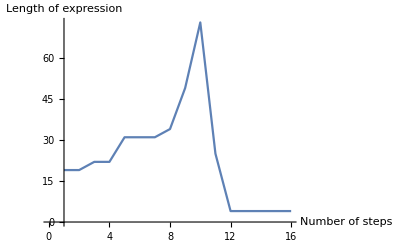

```mathematica
SKPlot[s[s[s]][s][s][s][k],15]
```

It is evident from the graph that this combinator halts at 12 steps.

#### Random SK combinators

To empirically study SK combinators, we need a function to randomly generate them. Two methods to do this were found:

```mathematica
RecursiveRandomSKExpr[0,current_]:=current;
RecursiveRandomSKExpr[depth_,current_]:= 
RecursiveRandomSKExpr[depth-1,
RandomChoice[{
RandomChoice[{s,k}][current],
current[RecursiveRandomSKExpr[depth-1,RandomChoice[{s,k}]]]
}]
];
RecursiveRandomSKExpr[depth_Integer]:=RecursiveRandomSKExpr[depth,RandomChoice[{s,k}]];
```

A recursive method, repeatedly appending either a combinator to the ‘head’ of the expression or a randomly generated combinator expression to the ‘tail’ of the expression. (Hennigan)

```mathematica
replaceWithList[expr_,pattern_,replaceWith_]:=ReplacePart[expr,Thread[Position[expr,pattern]->replaceWith]];
treeToFunctions[tree_]:=ReplaceRepeated[tree,{x_,y_}:>x[y]];
randomTree[leafCount_]:=Nest[ReplacePart[#,RandomChoice[Position[#,x]]->{x,x}]&,{x,x},leafCount-2];
RandomSKExpr[leafCount_]:=treeToFunctions[replaceWithList[randomTree[leafCount],x,RandomChoice[{s,k},leafCount]]];
```

Random combinator generation based on generation of binary trees - each combinator can be expressed as a binary tree with leaves ‘S’ or ‘K’. (Parfitt, 2017)

While the first method gives a large spread of combinators with a variety of lengths, and is potentially more efficient, for the purposes of this exploration the second is more useful, as it limits the combinators generated to a smaller, more controllable sample space (for a given leaf size).

### Halting Graphs

All combinators of leaf sizes up to size 6 evolve to fixed points (NKS):

```mathematica
exprs = Table[RandomSKExpr[6],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

-Graphics-

10 randomly generated combinators of size 6, with their lengths plotted until n=40.

As the leaf size increases, combinators take longer to halt, and some show exponential growth:

```mathematica
exprs = Table[RandomSKExpr[10],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

-Graphics-

10 randomly generated combinators of size 10, with their lengths plotted until n=20.

```mathematica
exprs = Table[RandomSKExpr[30],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]
```

-Graphics-

10 randomly generated combinators of size 30, with their lengths plotted until n=40.

```mathematica
CloudEvaluate[exprs = Table[RandomSKExpr[50],10];
ImageCollage[Table[ListLinePlot[SKLengths[exprs[[n]],40]],{n,10}],Background->White]]
```

-Graphics-

10 randomly generated combinators of size 50, with their lengths plotted until n=40.

After evaluating a number of these combinators, it appears that they tend to either halt or grow exponentially - some sources (Parfitt, 2017) reference linear growth combinators, however none of these have been encountered as yet.

### Halting Times

With a random sample of combinators, we can plot a cumulative frequency graph of the number of combinators that have halted at a given number of steps:

```mathematica
SKHaltLength[expr_,n_]:=Module[{x},
x=Length[SKEvaluateUntilHalt[expr,n+1]];
If[x>n,False,x]
]
```

Returns the number of steps it takes the combinator expr to halt; if expr does not halt within n steps, returns False.

```mathematica
GenerateHaltByTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[SKHaltLength[exprs[[n]],iterations],{n,number}],n];
Return[lengths]
]
```

Generates a table of the halt lengths of number random combinator expressions (False if they do not halt within iterations steps) with leaf size depth.

```mathematica
GenerateHaltData[depth_,iterations_,number_]:=Module[{haltbytable,vals},
haltbytable = GenerateHaltByTable[depth,iterations,number];
vals = BinCounts[Sort[haltbytable],{1,iterations+1,1}];
Table[Total[vals[[1;;n]]],{n,1,Length[vals]}]
]
```

Generates a table of the number of number random combinator expressions (False if they do not halt within iterations steps) with leaf size depth that have halted after a given number of steps

```mathematica
GenerateHaltGraph[depth_,iterations_,number_]:=Module[{cumulative,f},
cumulative=GenerateHaltData[depth,iterations,number];
f=Interpolation[cumulative];
{ListLinePlot[cumulative,PlotRange->{Automatic,{0,number}},GridLines->{{},{number}},Epilog-> {Red,Dashed,Line[{{0,cumulative[[-1]]},{number,cumulative[[-1]]}}]},AxesOrigin->{1,0},AxesLabel->{"Number of steps","Number of combinators halted"}],cumulative[[-1]]}
]
```

Plots a graph of the above data.

#### Halting Graphs

We analyse halt graphs of random samples of 1000 combinators (to depth 30):

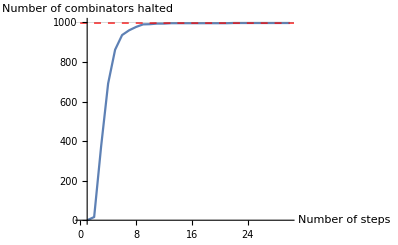
{-Graphics-,997}

```mathematica
CloudEvaluate[GenerateHaltGraph[10,30,1000]]
```

Leaf size 10: almost all combinators in the sample (997) have halted (99.7%).

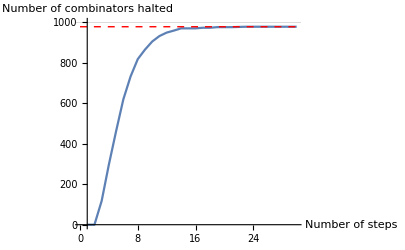
{-Graphics-,979}

```mathematica
CloudEvaluate[GenerateHaltGraph[20,30,1000]]
```

Leaf size 20: 979 combinators in the sample have halted (97.9%).

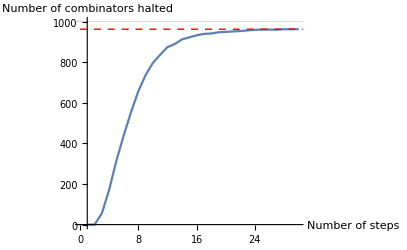
{-Graphics-,962}

```mathematica
CloudEvaluate[GenerateHaltGraph[30,30,1000]]
```

Leaf size 30: 962 combinators in the sample have halted (96.2%).

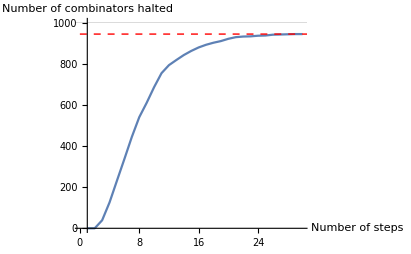
{-Graphics-,944}

```mathematica
CloudEvaluate[GenerateHaltGraph[40,30,1000]]
```

Leaf size 40: 944 combinators in the sample have halted (94.4%).

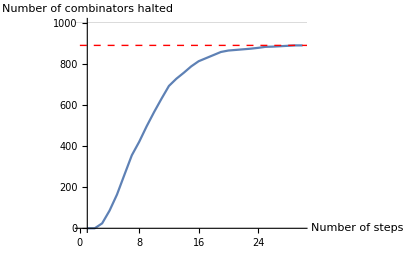
{-Graphics-,889}

```mathematica
CloudEvaluate[GenerateHaltGraph[50,30,1000]]
```

Leaf size 50: 889 combinators in the sample have halted (88.9%).

Evidently, the rate of halting of combinators in the sample decreases as number of steps increases - the gradient of the graph is decreasing. As the graph levels out at around 30 steps, we will assume that the number of halting combinators will not increase significantly beyond this point. 
As the leaf size increases, fewer combinators in the sample have halted by 30 steps - however, the graph still levels out, suggesting most of the combinators which have not halted by this point will never halt.

#### Halting Times and Leaf Size

We can plot a graph of the number of halted combinators against leaf size:

```mathematica
CloudEvaluate[ListLinePlot[Table[{n,GenerateHaltGraph[n,30,1000][[2]]},{n,5,50,1}]]]
```

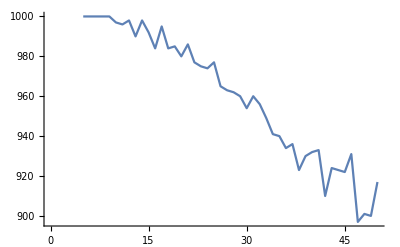

A graph to show the number of combinators which halt within 30 steps in each of 45 random samples of 1000 combinators, with leaf size varying from 5 to 50.

This graph shows that, despite random variation, the number of halted combinators decreases as the leaf size increases: curve fitting suggests that this follows a negative quadratic function.

```mathematica
FitData[data_,func_]:=Module[{fitd},fitd={Fit[data[[1,2,3,4,1]],func,x]};{fitd,Show[ListPlot[data[[1,2,3,4,1]],PlotStyle->Red],Plot[fitd,{x,5,50}]]}]
```

A curve-fitting function: plots the curve of best fit for data with some combination of functions func.

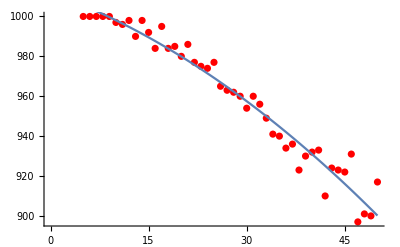
{{1012.07-1.18915 x-0.0209805 x^2},-Graphics-}

```mathematica
FitData[-Graphics-,{1,x,x^2}]
```

Curve-fitting on the data with a quadratic function yields a reasonably accurate curve of best fit.

## Machine Learning Analysis of SK Combinators

The graphs above suggest that the majority of halting SK combinators with leaf size <=50 will halt before ~30 steps. Thus we can state that, for a randomly chosen combinator, it is likely that if it does not halt before 40 steps, it will never halt. Unfortunately a lack of time prohibited a formal analysis of this, in the vein of Lathrop’s work - this is an area for future research.

We attempt to use modern machine learning methods to predict the likelihood of a given SK combinator expression halting before 40 steps:

### Dataset Generation

We implement a function GenerateTable to produce tables of random SK expressions:

```mathematica
SKHaltLength[expr_,n_]:=Module[{x},
x=Length[SKEvaluateUntilHalt[expr,n+1]];
If[x>n,False,x]
]
```

Returns the number of steps expr takes to halt if the given expression expr halts within the limit given (limit), otherwise returns False

```mathematica
GenerateTable[depth_,iterations_,number_]:=Module[{exprs,lengths},
exprs = Monitor[Table[RandomSKExpr[depth],{n,number}],n];
lengths = Monitor[Table[exprs[[n]]-> SKHaltLength[exprs[[n]],iterations],{n,number}],n];
lengths = DeleteDuplicates[lengths];
Return[lengths]
]
```

Returns a list of number expressions with leaf size depth whose elements are associations with key expression and value number of steps taken to halt if the expression halts within iterations steps, otherwise False.

GenerateTable simply returns tables random SK expressions - as seen earlier, these tend to be heavily skewed datasets as around 90% of random expressions generated will halt. Thus we must process this dataset to create a balanced training dataset: this is done with the function CreateTrainingData:

```mathematica
CreateTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,Train},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
Train = Join[HaltTrain,NoHalt];
Return[Train]
];
```

Counts the number of non-halting combinators in var (assumption is this is less than number of halting combinators), selects a random sample of halting combinators of this length and concatenates the lists.

```mathematica
ConvertSKTableToString[sktable_]:=Table[ToString[sktable[[n,1]]]-> sktable[[n,2]],{n,1,Length[sktable]}];
```

Converts SK expressions in a table generated with GenerateTable to strings

We also implement a function to create rasterised training data (where instead of an individual SK combinator associated with either True or False, an image of the first 5 steps of evaluation of the combinator is associated with either True or False):

```mathematica
CreateRasterizedTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,HaltTrainRaster,NoHaltTrainRaster,RasterTrain},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
Return[RasterTrain]
];
```

Counts the number of non-halting combinators in var (assumption is this is less than number of halting combinators), selects a random sample of halting combinators of this length, evaluates and generates images of both halting and non-halting combinators and processes them into training data (image->True/False).

### Markov Classification

#### Training

As a first attempt, we generate 2000 random SK expressions with depth 5, 2000 expressions with depth 10 ... 2000 expressions with depth 50, evaluated up to 40 steps:

```mathematica
lengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]]
```

We convert all non-False halt lengths to ‘True’:

```mathematica
lengths = lengths/.(a_->b_)/;!(b===False):> (a->True);
```

We process the data and train a classifier using the Markov method:

```mathematica
TrainingData = CreateTrainingData[lengths];
TrainingData2 = ConvertSKTableToString[TrainingData];
```

```mathematica
HaltClassifier1 = Classify[TrainingData2,Method->"Markov"]
```

ClassifierFunction[…]

#### Testing

We must now generate test data, using the same parameters for generating random combinators:

```mathematica
testlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]]
testlengths = testlengths/.(a_->b_)/;!(b===False):> (a->True);
TestData = CreateTrainingData[testlengths];
TestData2 = ConvertSKTableToString[TestData];
```

The classifier can now be assessed for accuracy using this data:

```mathematica
TestClassifier1 = ClassifierMeasurements[HaltClassifier1,TestData2]
```

ClassifierMeasurementsObject[…]

#### Evaluation

A machine learning solution to this problem is only useful if the accuracy is greater than 0.5 (i.e. more accurate than a random coin flip). We test the accuracy of the classifier:

```mathematica
TestClassifier1["Accuracy"]
```

0.755158

This, while not outstanding, is passable for a first attempt. We find the training accuracy:

```mathematica
ClassifierInformation[HaltClassifier1]
```

Classifier information
Input type | Text
Classes | ,,FalseTrue
Method | Markov
Accuracy | 71.3 % ± 3.8 %
Loss | 0.539 ± 0.033
Single evaluation time | 7.15 ms/example
Batch evaluation speed | 699. examples/s
Classifier memory | 134. kB
Training examples used | 1456 examples
Training time | 14.6 s
 |

The training accuracy (71.3%) is slightly lower than the testing accuracy (75.5%) - this is surprising, and is probably due to a ‘lucky’ testing dataset chosen.

We calculate some statistics from a confusion matrix plot:

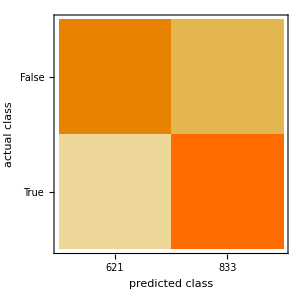

```mathematica
TestClassifier1["ConfusionMatrixPlot"]
```

Accuracy: 0.76
Misclassification rate: 0.24

Precision (halt): 0.722 (when ‘halt’ is predicted, how often is it correct?)
True Positive Rate: 0.83 (when the combinator halts, how often is it classified as halting?)
False Positive Rate: 0.32 (when the combinator doesn’t halt, how often is it classified as halting?)

Precision (non-halt): 0.799 (when ‘non halt’ is predicted, how often is it correct?)
True Negative Rate: 0.68 (when the combinator doesn’t halt, how often is it classified as not halting?)
False Negative Rate: 0.17 (when the combinator halts, how often is it classified as not halting?)

A confusion matrix plot shows that the true positive rate is larger than the true negative rate - this would suggest that it is easier for the model to tell when an expression halts than when an expression does not halt. This could be due to the model detecting features suggesting very short run time in the initial string - for instance, a combinator k[k][<expression>] would evaluate immediately to k and halt - however, these ‘obvious’ features are very rare.

### Random Forest Classification on Rasterised Expression Images

Analysing strings alone, without any information about how they are actually structured or how they might evaluate, could well be a flawed method - one might argue that, in order to predict halting, one would need more information about how the program runs. Hence, another possible method is to generate a dataset of visualisations of the first 5 steps of a combinator’s evaluation as follows:

```mathematica
SKRasterize[RandomSKExpr[50],5]
```

-Graphics-

and feed these into a machine learning model. Although it might seem that this method is pointless - we are already evaluating the combinators to 5 steps, and we are training a model on a database of combinators evaluated to 40 steps to predict if a combinator will halt in <=40 steps, the point of the exercise is less to create a useful resource than to investigate the feasibility of applying machine learning to this type of problem. If more computational power was available, a dataset of combinators evaluated to 100 steps (when even more combinators will have halted) could be created: in such a case a machine learning model to predict whether or not a combinator will halt in <=100 steps would be a practical approach as the time taken to evaluate a combinator to 100 steps is exponentially longer than that taken to evaluate a combinator to 5 steps.

#### Training

We generate a dataset of 2000 random SK expressions with depth 5, 2000 expressions with depth 10 ... 2000 expressions with depth 50, evaluated up to 40 steps:

```mathematica
rasterizedlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]];
```

In order to train a model on rasterised images, we must evaluate all SK expressions in the dataset to 5 steps and generate rasterised images of these:

```mathematica
RasterizedTrainingData = CreateRasterizedTrainingData[rasterizedlengths];
```

We then train a classifier on this data:

```mathematica
RasterizeClassifier=Classify[RasterizedTrainingData,Method->"RandomForest"]
```

ClassifierFunction[…]

#### Testing

We must now generate test data, using the same parameters for generating random training data:

```mathematica
testrasterizedlengths = Flatten[Table[GenerateTable[n,40,2000],{n,5,50,5}]];
testrasterizedlengths = testrasterizedlengths/.(a_->b_)/;!(b===False):> (a->True);
TestRasterizedData = CreateRasterizedTrainingData[testrasterizedlengths];
```

The classifier can now be assessed for accuracy using this data:

```mathematica
TestRasterizeClassifier=ClassifierMeasurements[RasterizeClassifier,TestRasterizedData]
```

ClassifierMeasurementsObject[…]

#### Evaluation

A machine learning solution to this problem is only useful if the accuracy is greater than 0.5 (i.e. more accurate than a random coin flip). We test the accuracy of the classifier:

```mathematica
TestRasterizeClassifier["Accuracy"]
```

0.876891

This is significantly better than the Markov approach (75.5%). We find the training accuracy:

```mathematica
ClassifierInformation[RasterizeClassifier]
```

Classifier information
Input type | Image
Classes | ,,FalseTrue
Method | RandomForest
Accuracy | 85.5 % ± 3. %
Loss | 0.409 ± 0.027
Single evaluation time | 6.17 ms/example
Batch evaluation speed | 735. examples/s
Classifier memory | 332. kB
Training examples used | 1456 examples
Training time | 9.83 s
 |

Again, the training accuracy (85.5%) is slightly lower than the testing accuracy (87.7%).

We calculate some statistics from a confusion matrix plot:

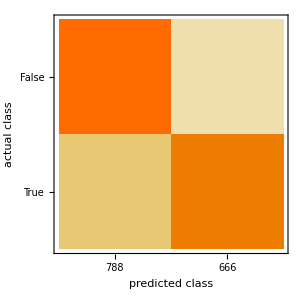

```mathematica
TestRasterizeClassifier["ConfusionMatrixPlot"]
```

Accuracy: 0.88
Misclassification rate: 0.12

Precision (halt): 0.911 (when ‘halt’ is predicted, how often is it correct?)
True Positive Rate: 0.83 (when the combinator halts, how often is it classified as halting?)
False Positive Rate: 0.08 (when the combinator doesn’t halt, how often is it classified as halting?)

Precision (non-halt): 0.848 (when ‘non halt’ is predicted, how often is it correct?)
True Negative Rate: 0.92 (when the combinator doesn’t halt, how often is it classified as not halting?)
False Negative Rate: 0.17 (when the combinator halts, how often is it classified as not halting?)

A confusion matrix plot shows that the false negative rate is larger than the false positive rate - this would suggest that it is easier for the model to tell when an expression halts than when an expression does not halt. The precision for halting is much higher than the precision for non-halting, indicating that if the model suggests a program will halt, this is much more likely to be correct than if it suggested that the program would not halt. An (oversimplified) way to look at this intuitively is to examine some graphs of lengths of random combinators:

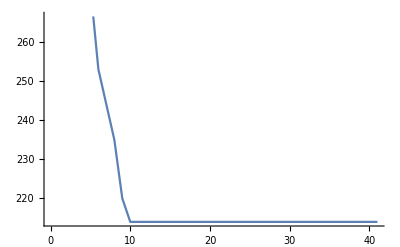
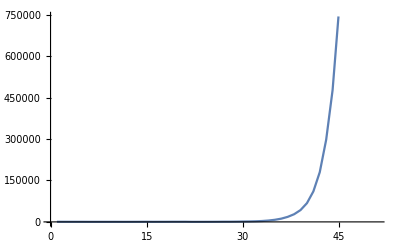
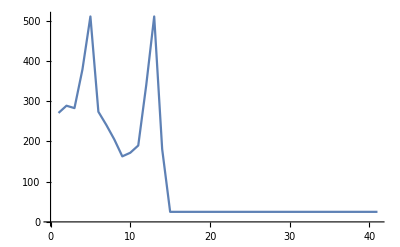
-Graphics-
Looking at combinators that halt (combinators for which the graph flattens out), some combinators ‘definitely halt’ - their length decreases until the graph flattens out:
-Graphics- → ‘definitely halts’ (1)
Some combinators have length that increases exponentially:
-Graphics- → ‘possibly non-halting’ (2)
And some combinators appear to have increasing length but suddenly decrease:
-Graphics- → ‘possibly non-halting’ (3)

We do not know which features of the rasterised graphic the machine learning model extracts to make its prediction, but if, say, it was classifying based purely on length of the graphic, it would identify combinators like (1) as ‘definitely halting’, but would not necessarily be able to distinguish between combinators like (2) and combinators like (3), which both appear to be non-halting initially.

On a similar note, some functional programming languages (e.g. Agda - [7]) have the ability to classify a function as 'definitely halting' or 'possibly non-halting', just like our classifier, whose dataset is trained on functions that either 'definitely halt' (halt in <=40 steps) or are 'possibly non-halting' (do not halt in <=40 steps - might halt later).

### Table of Comparison

| Markov on Strings | Random Forest on Images
Confusion Matrix | -Graphics- | -Graphics-
Accuracy | 0.76 | 0.88
Misclassification rate | 0.24 | 0.12
Precision (halt) | 0.722 | 0.911
True Positive Rate | 0.83 | 0.83
False Positive Rate | 0.32 | 0.08
Precision (non-halt) | 0.799 | 0.848
True Negative Rate | 0.68 | 0.92
False Negative Rate | 0.17 | 0.17

## Conclusions and Further Work

### Conclusions

The results of this exploration were somewhat surprising, in that a machine learning approach to determining whether or not a program will terminate appears to some extent viable - out of all the methods attempted, the random forest classifier applied to a rasterised image of the first five steps of the evaluation of a combinator achieved the highest accuracy of 0.88 on a test dataset of 1454 random SK combinator expressions. Note, though, that what is actually being determined here is whether or not a combinator will halt before some n steps (here, n=40) - we are classifying between combinators that ‘definitely halt’ and combinators which are ‘possibly non-halting’.

### Microsite

As an extension to this project, a Wolfram microsite was created and is accessible at https://www.wolframcloud.com/objects/euan.l.y.ong/SKCombinators - within this microsite, a user can view a rasterised image of a combinator, a graph of the length of the combinator as it is evaluated, a statistical analysis of halting time relative to other combinators with the same leaf size and a machine learning prediction of whether or not the combinator will halt within 40 steps.

A screenshot of the microsite evaluating a random SK combinator expression

### Implications, Limitations and Further Work

Although the halting problem is undecidable, the field of termination analysis - attempting to determine whether or not a given program will eventually terminate - has a variety of applications, for instance in program verification. Machine learning approaches to this problem would not only help explore this field in new ways but could also be implemented in, for instance, software debuggers.

The principal limitations of this method are that we are only predicting whether or not a combinator will halt in a finite number k of steps - while this could be a sensible idea if k is large, at present this system is very impractical due to small datasets and a small value of k used to train the classifier (k = 40). Another issue with the machine learning technique used is that the visualisations have different dimensions (longer combinators will generate longer images), and when the images are preprocessed and resized before being fed into the random forest model, downsampling/upsampling can lead to loss of data decreasing the accuracy of the model.

From a machine learning perspective, attempts at analysis of the rasterised images with a neural network could well prove fruitful, as would an implementation of a vector representation of syntax trees to allow the structure of SK combinators (nesting combinators) to be accurately extracted by a machine learning model.

Future theoretical research could include a deeper exploration of Lathrop’s probabilistic method of determining k, an investigation of the ‘halting’ features the machine learning model is looking for within the rasterised images, a more general analysis of SK combinators (proofs of halting / non-halting for certain expressions, for instance) to uncover deeper patterns, or even an extension of the analysis carried out in the microsite to lambda calculus expressions (which can be transformed to an ‘equivalent’ SK combinator expression).

Acknowledgements

We thank the mentors at the 2018 Wolfram High School Summer Camp - Andrea Griffin, Chip Hurst, Rick Hennigan, Michael Kaminsky, Robert Morris, Katie Orenstein, Christian Pasquel, Dariia Porechna and Douglas Smith - for their help and support writing this paper.

References

A. Church and J. B. Rosser: Some properties of conversion. Transactions of the American Mathematical Society, 39 (3): 472–482, 2018

R. H. Lathrop: On the learnability of the uncomputable. ICML 1996: 302-309.

C. S. Calude and M. Dumitrescu: A probabilistic anytime algorithm for the halting problem. Computability 7(2-3): 259-271, 2018.

L. G. Valiant: A theory of the learnable. Communications of the Association for Computing Machinery 27, (11): 1134-1142, 1984.

S. Wolfram: A New Kind of Science. 1121-1122, 2002.

E. Parfitt: Ways that combinators evaluate from the Wolfram Community—A Wolfram Web Resource. (2017)
http://community.wolfram.com/groups/-/m/t/965400

S-C Mu: Agda.Termination.Termination http://www.iis.sinica.edu.tw/~scm/Agda/Agda-Termination-Termination.html